```mathematica
StringToSet[s_]:=Block[{result},
Table[FromDigits[StringTake[s,{k}]],{k,1,StringLength[s]}]
]
```

```mathematica
ApplySolution[g_,symbol_]:=Block[{blocks,edges={},vertices,h,vertex},
blocks=StringSplit[ StringDrop[SymbolName[symbol],1],"x"];
Table[
vertices=StringToSet[b];
Table[edges=Append[edges,s[[1]]<->s[[2]]],{s,Subsets[vertices,{2}]}]
,{b,Select[blocks,StringLength[#]>1&]}
];
vertices={};
Table[
vertex=FromDigits[b];
vertices=Append[vertices,vertex]
,{b,Select[blocks,StringLength[#]==1&]}
];
h=EdgeAdd[g,edges];
Graph[h,GraphHighlight->edges,VertexStyle->Map[#->Red&,vertices],VertexSize->Map[#->Large&,vertices], GraphHighlightStyle->"Thick"]
]
```

```mathematica
SymbolToKey2[s_]:=Block[{tail=StringDrop[s,1], temp},
temp=ToExpression[tail];
If[!NumericQ[temp],
tail,
temp]
]
```

```mathematica
SetComp[s1_,s2_]:=Block[{l=Min[Length[s1],Length[s2]],i},
For[i=1,i≤l,i++,
If[s1[[i]]≠s2[[i]],
Return[s1[[i]]>s2[[i]]]
]
];
Return[Length[s1]>Length[s2]]
]
```

```mathematica
SymbolComp3[x_,y_]:=Block[{n1=SymbolName[x],n2=SymbolName[y],a,b,h1,h2,l1,l2},
h1=StringDrop[n1,1];
h2=StringDrop[n2,1];
l1=Sort[Map[StringLength[#]&,StringSplit[h1,"x"]],Greater];
l2=Sort[Map[StringLength[#]&,StringSplit[h2,"x"]],Greater];
Return[SetComp[l1,l2]]
]
```

```mathematica
allGraphs5FakeAtomKeys=Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofournull"]]]==1&];Length[allGraphs5FakeAtomKeys]
```

52

```mathematica
Table[allGraphs5[k,"graph"],{k,allGraphs5FakeAtomKeys}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
repFake5=Table[allGraphs5[k,"colofournull"]->allGraphs5[k,"graph"],{k,allGraphs5FakeAtomKeys}];
```

```mathematica
Table[Framed[Labeled[allGraphs5[k,"graph"],Style[k,Red]]->Column[{Prepend[Table[ApplySolution[allGraphs5[k,"graph"],symb],{symb,Sort[ListofVars[allGraphs5[k,"colofour"]],SymbolComp3[#1,#2]&]}],ChromaticPolynomial[allGraphs5[k,"graph"],3]]}]],{k,RandomSample[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&ConnectedGraphQ[allGraphs5[#,"graph"]]&&MaximalPlanarQ[allGraphs5[#,"graph"]]&],10]}]//TableForm
```

-Graphics-29281→{0,-Graphics-,-Graphics-}
-Graphics-29521→{0,-Graphics-,-Graphics-}
-Graphics-22963→{0,-Graphics-,-Graphics-}
-Graphics-28795→{0,-Graphics-,-Graphics-}
-Graphics-29443→{0,-Graphics-,-Graphics-}
-Graphics-27337→{0,-Graphics-,-Graphics-}
-Graphics-29523→{0,-Graphics-,-Graphics-}
-Graphics-29497→{0,-Graphics-,-Graphics-}
-Graphics-9841→{0,-Graphics-,-Graphics-}
-Graphics-29515→{0,-Graphics-,-Graphics-}

```mathematica
Table[Framed[Labeled[allGraphs6[k,"graph"],Style[k,Red]]->Column[{Prepend[Table[ApplySolution[allGraphs6[k,"graph"],symb],{symb,Sort[ListofVars[allGraphs6[k,"colofour"]],SymbolComp3[#1,#2]&]}],ChromaticPolynomial[allGraphs6[k,"graph"],3]]}]],{k,RandomSample[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&ConnectedGraphQ[allGraphs6[#,"graph"]]&&MaximalPlanarQ[allGraphs6[#,"graph"]]&],20]}]//TableForm
```

-Graphics-6640798→{6,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7165704→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7171534→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7174200→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7167568→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-2384914→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-6643002→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-2207776→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7108840→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-2391400→{6,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-6623328→{6,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-6938176→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7171528→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-2389216→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7115392→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7154040→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-5579392→{6,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7154038→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7112488→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-7167862→{0,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

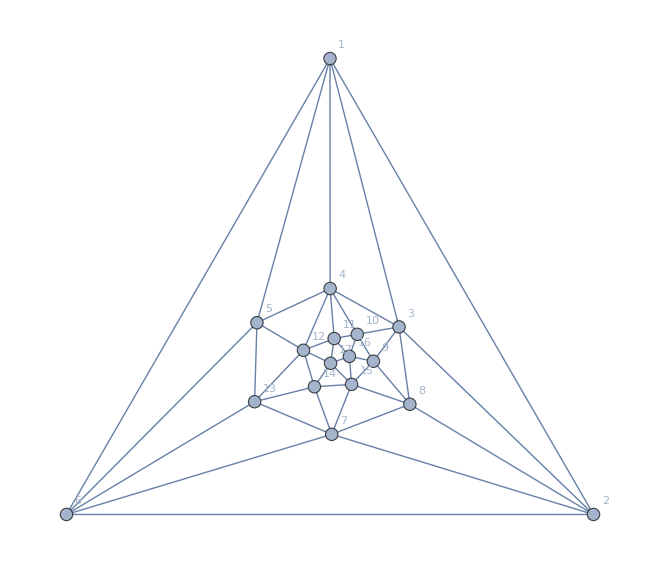

```mathematica
Graph[plantri[[8]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```